## THIS PUBLIC DOMAIN SOFTWARE WAS PRODUCED BY AN EMPLOYEE OF U.S. GOVERNMENT

# Retro-Preferential Processes with Sporadic Reports

## R. W. R. Darling U.S. Department of Defense

Tue 2 May 2017 20:16:32

.1fINSTRUCTIONS :
 1. Begin by evaluating the  initialization cells (Evaluation Menu), which contain the basic functions of Section 1.
 2. Decide on Global Parameter settings in Section 1.1
 3. Go to Section 2 and run the orange box in Section 2.1. Now you have a full set of simulated data.
 4. All the other sections contain optional graphics and diagnostics.

```mathematica
LIGHT BLUE background: FUNCTIONS
```

```mathematica
LIGHT ORANGE background: invocations of functions
```

## Section. Functions

### Section.Subsection GLOBAL PARAMETERS

```mathematica
nPlacesExceptZero = 300; (* number of points ≠ (0,0); hence nPlacesExceptZero + 1 is true number *)
θ = 2.0; (* agoraphobic clump frequency parameter *)
ρ = 0.8; (* reciprocal of Hausdorff dimension *)
ϕ = 13.75; (* parameter > 0 *)
nSteps = 430; (* desired # steps, which is Length[trajectory] - 1 *)
(* REPORT MODEL ...................................................... *)
maxSpeed = 1.0;
αMotion = 0.55; (* Pareto exponent *)
cMotion = 10.0; (* multiple of the minimum *)
sReports = 1.5; (* Zipf exponent *)
cReports = 50; (* Zipf maximum *)
ηReports = 0.9; (* self-declared arbitrary; Bernoulli rate at which a sojourn generates ≥1 report *)
βSojourn = 0.287; (* Pareto exponent *)
minSojourn  = 1.0/(24.0*3600.0); (* 1 seconds in unit of days *)
cSojourn = 6.0*3600.0; (* 1/4 day as multiple of the minimum *)
seasonalα = 4.17; (* for daily seasonality adjustment *)
seasonalβ = 2.98; (* for daily seasonality adjustment *)
corruptionRate = 0.025 ;(* proportion of locations which will be replaced by a random location *)
```

### Section.Subsection AGORAPHOBIC - Hard Threshold: Rejection sampling of points Unit Disk, based on time & distance to nearest previous point

```mathematica
samplePointUnitDisk[]:= Module[{r,ζ},
r=Sqrt[RandomReal[]];
ζ=RandomReal[{0.0, 2*Pi}];
(* Random point in unit disk *)
Return[ {r*Cos[ζ], r*Sin[ζ]}];
];

(* r > 1/2. Typically r = 1 *)
agoraphobicPointsHardThreshold[n_,θ_, r_]:=Module[{pointSet,edgeSet,parent, child ,j,newClumpProbability,startNewClump,accept,radius,neighborCount  },
pointSet={{0.0,0.0}};
edgeSet = {};
For[j=1, j≤n,j++,
newClumpProbability = θ/(θ+j-1);
(* Bernoulli Trial *)
startNewClump = (RandomReal[] < newClumpProbability );
If[startNewClump, 
child = samplePointUnitDisk[];
AppendTo[pointSet, child];
AppendTo[edgeSet , DirectedEdge[{0.0,0.0},child]];
];
(* Sample point in existing clump *)
If[¬startNewClump, 
accept = False;
While[¬accept,
parent = RandomChoice[pointSet];
radius = N[Power[j,-r]];
child = parent+radius *samplePointUnitDisk[];
neighborCount = Length[Select[pointSet, (Norm[child - #] ≤ radius)&] ];
accept = (RandomReal[] <  1.0/neighborCount);
];
AppendTo[pointSet, child];
AppendTo[edgeSet , DirectedEdge[parent,child]];
];
];
Return[edgeSet ];
];
```

{7.82281,Null}

{1001,1001}

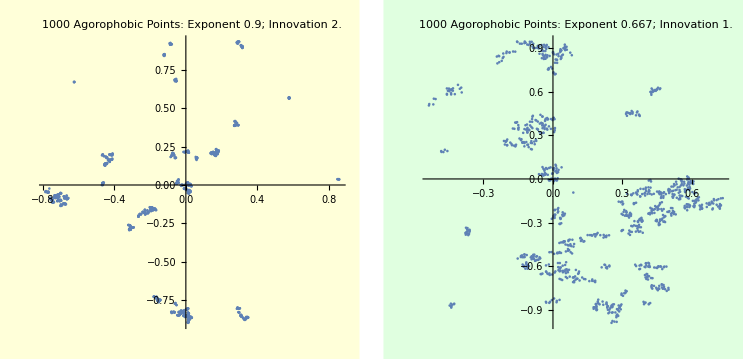

```mathematica
n1 = 1000;
θ1 =2.0;
r1 =0.9;
θ2 = 1.0;
r2 = 0.667;
Timing[
Gh1=Graph[agoraphobicPointsHardThreshold[n1,θ1,r1]];
Gh2=Graph[agoraphobicPointsHardThreshold[n1,θ1,r2]];
]
Map[VertexCount, {Gh1,Gh2}]

lprh1 = ListPlot[VertexList[Gh1] , Background->LightYellow,AspectRatio->1.0,
PlotLabel->Row[{n1," Agorophobic Points: Exponent ",r1 , "; Innovation ", θ1  }]];
lprh2 = ListPlot[VertexList[Gh2] , Background->LightGreen,AspectRatio->1.0,
PlotLabel->Row[{n1," Agorophobic Points: Exponent ",r2 , "; Innovation ", θ2   }]];
GraphicsRow[{lprh1,lprh2}]
```

### Section.Subsection RETRO-PREFERENTIAL: Visit List Based on Past Frequency & Inverse Distance Weighted Process

```mathematica
(* X = list of points; ϕ parameter, such as 13.0; s = nSteps *) 
(* Output: list consisting of 1 and s subsequent indices, referring to X *)
retropreferentialMotion[X_,ϕ_,s_]:=Module[{n,idm,j,i, trajectory ,place ,visitCounts,past, f ,outwardStep ,transitionVector ,ptVector },
n = Length[X];
(* inverse distance array *)
idm = Table[If[i≠j, 1.0/Dot[X[[i]] - X[[j]] ,X[[i]] - X[[j]]  ],0.0], {i, 1, n}, {j,1, n}];
(* Initialize *)
trajectory = {1}; (* list of indices of locations visited: start at 1 *)
place = Last[trajectory]; (* present location *)
visitCounts = Table[0, {n}];
visitCounts [[1]] = 1;
(* augment the list *)
While[Length[trajectory]≤s,
past=Union[trajectory]; (* set of locations visited *)
(* Probability of an outward step -- gives size of "past" as sqrt[time]*)
f= ϕ/(Length[past] -1 + ϕ);
outwardStep = (RandomReal[] <f);
(* When revisiting previous place, weight by (# previous visits) ÷ (squared distance from place) *)
transitionVector = If[outwardStep, 
Table[If[MemberQ[past,j], 0.0, idm[[place, j]] ], {j, 1, n}],
Table[If[MemberQ[past,j], visitCounts [[j]]*idm[[place, j]] ,0.0], {j, 1, n}]
];
ptVector = transitionVector /Total[transitionVector ];
(* Random transition *)
place = First[Flatten[ Position[RandomVariate[MultinomialDistribution[1, ptVector] ], 1] ] ];
AppendTo[trajectory, place];
visitCounts [[place]] ++;
];
Return[trajectory];
];
```

### Section.Subsection Seasonality Adjustment

```mathematica
(* Beta inverse CDF during day -- see global parameter set *)
inverseDF = InverseCDF[BetaDistribution[seasonalα,seasonalβ],#]&;
seasonAdjust[t_]:= Floor[t]+inverseDF[t - Floor[t] ] ;
```

### Section.Subsection SPORADIC-REPORTER: Gives Report List, and Also True Sojourns

```mathematica
(* Requires list X of points from AGORAPHOBIC and trajectory from RETRO-PREFERENTIAL, and global parameter set *)
sporadicReporter[X_,trajectory_]:=Module[{distanceList, γ,Z,atLeastOneReport,uncensoredReportCounts, κ,reportCounts,fineIntervals,Y,Ycumulative,Zcumulative,sojournStarts,corruptedTrajectory,sporadicReports ,sojournEnds,sojournHistory },

(* Simulate Motion Times(Subscript[Z, i])-Truncated Pareto *)
distanceList=Map[Norm, Differences[X[[trajectory]] ] ];
γ = 1.0 - (1.0/cMotion)^αMotion;
Z = Table[(1.0/maxSpeed)*distanceList[[j]]/((1.0 - γ*RandomReal[])^(1.0/αMotion)), {j, 1, Length[trajectory]-1} ];

(* Simulate Report Counts per Sojourn(Subscript[R, i]),& Gaps(Subscript[U, j]^k)During Sojourn-Truncated Zipf/Pareto *)
atLeastOneReport = RandomVariate[BernoulliDistribution[ηReports],Length[trajectory] ];
uncensoredReportCounts = RandomVariate[ZipfDistribution[cReports,sReports - 1], Length[trajectory]];
reportCounts = atLeastOneReport*uncensoredReportCounts ;
κ=1.0 - (1.0/cSojourn)^βSojourn;
fineIntervals = Table[
(* simulate truncated Pareto *)
Table[minSojourn/((1.0 - κ*RandomReal[])^(1.0/βSojourn)), {reportCounts[[j]]+1} ], {j, 1, Length[trajectory] }];

(* corrupt the trajectory *)
corruptedTrajectory = Table[If[RandomReal[]< corruptionRate, RandomInteger[{1, Length[X]}],trajectory[[j]] ],
{j, 1, Length[trajectory] }];

(* Simulate Entire Report Set,Seasonally Adjusted, with Corrupted Location Values *)
(* sojourn intervals are obtained by summing sets of fine intervals *)
Y = Map[Total, fineIntervals ];
Ycumulative = Accumulate[Y];
Zcumulative = Accumulate[Z];
(* arrival times *)
sojournStarts = Prepend[Drop[Ycumulative, -1]+Zcumulative , 0.0];
sporadicReports =Flatten[ Table[If[reportCounts[[j]]≥1,
{seasonAdjust[sojournStarts [[j]]+fineIntervals[[j, k]] ],corruptedTrajectory[[j]]}], 
{j, 1, Length[trajectory]}, {k, 1, reportCounts[[j]] }], 1];

(* TRUTH: Reveal True Trajectory *)
(* departure times *)
sojournEnds = Prepend[Drop[Ycumulative, 1]+Zcumulative , First[Y]];
(* list of 3-ples of form (placeID, time-entered, time departed) *)
sojournHistory = Transpose[{trajectory,Map[seasonAdjust, sojournStarts], Map[seasonAdjust,sojournEnds]}];

(* OUTPUT *)
Return[{sporadicReports,sojournHistory}];
];
```

### Section.Subsection For n points, give sorted list of interpoint distances, as edges

```mathematica
(* X is a list of points in a Euclidean space *)
edgeWeights[X_]:= 
Sort[Map[
{UndirectedEdge[X[[First[#] ]], X[[Last[#] ]]  ], Norm[X[[First[#] ]]-X[[Last[#] ]] ]}&, Subsets[Range[Length[X]], {2}] ],#1[[2]]<#2[[2]]& ];
```

### Section.Subsection Kruskal’s Algorithm

```mathematica
(* Kruskal's Algorithm; n counts vertices; elements of ℰ are sorted edges of form {3<->18,0.3004} *)

minWeightSpanningTree[n_,ℰ_]:=Module[{G,edgePointer,endPoints },
(* insert lowest weight edge *)
G = Graph[ {ℰ[[1 , 1]] }];
edgePointer = 1;

(* Main loop of Kruskal's Algorithm. A spanning tree will have n-1 edges *)
While[(Length[EdgeList[G]]<n-1)∧(edgePointer<Length[ℰ]),
edgePointer ++;
(* vertices at ends of new edge candidate *)
endPoints =  {ℰ[[edgePointer , 1, 1]] , ℰ[[edgePointer , 1,2]] };
(* Add this edge unless both endpoints are in the same component of G *)
If[Max[Map[Length[Intersection[endPoints,#] ]&, ConnectedComponents[G] ] ]≤1, G=EdgeAdd[G, {ℰ[[edgePointer , 1]] }] ];
];
Return[G];
];
```

### Section.Subsection Fit Zipf’s Law to Count Data

```mathematica
(* Fitting Zipf Law to a list of integers X, all > 0, return table of expected values ≥ 1 *)
fitZipf[X_]:=Module[{ψ,sψ,f,kmax},
ψ= -N[Total[Log[X]]/Length[X] ];
sψ = FindRoot[Zeta'[s]/Zeta[s]==ψ, {s, 1.5}][[1, 2]];
f[k_]:=PDF[ZipfDistribution[sψ-1], k];
kmax = 1;
While[f[kmax]>1.0/Length[X], kmax++];
Return[{sψ, Table[{k, Length[X]*f[k]}, {k, 1, kmax}] }];
];
```

MLE of param = 1.50896

239

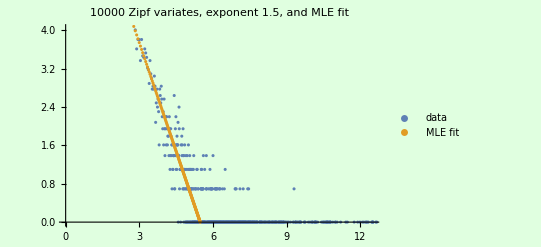

```mathematica
s0 = 1.5;
n0 = 10000;
Y=RandomVariate[ZipfDistribution[s0-1], n0];
data =Sort[Tally[Y] ];

{paramFit, dataFit} = fitZipf[Y];
Print["MLE of param = ", paramFit];
Length[dataFit]
ListPlot[{Log[data], Log[dataFit]},
Background->LightGreen,
PlotLegends->{"data", "MLE fit"},
PlotLabel->Row[{n0, " Zipf variates, exponent ", s0,", and MLE fit"  }]
]
```

### Section.Subsection Canonical Tree with Gaussian Edge Displacements

```mathematica
(* r > 1/2. Typically r = 1 *)
canonicalGaussTree[n_, r_]:=Module[{pointSet,edgeSet,parent, child ,j},
pointSet={{0.0,0.0}};
edgeSet = {};
For[j=1, j≤n,j++,
parent = RandomChoice[pointSet];
child = parent+RandomVariate[NormalDistribution[0, (1.0/j)^r], 2];
AppendTo[pointSet, child];
AppendTo[edgeSet , DirectedEdge[parent,child]];
];
Return[edgeSet ];
];
```

{6.15307,Null}

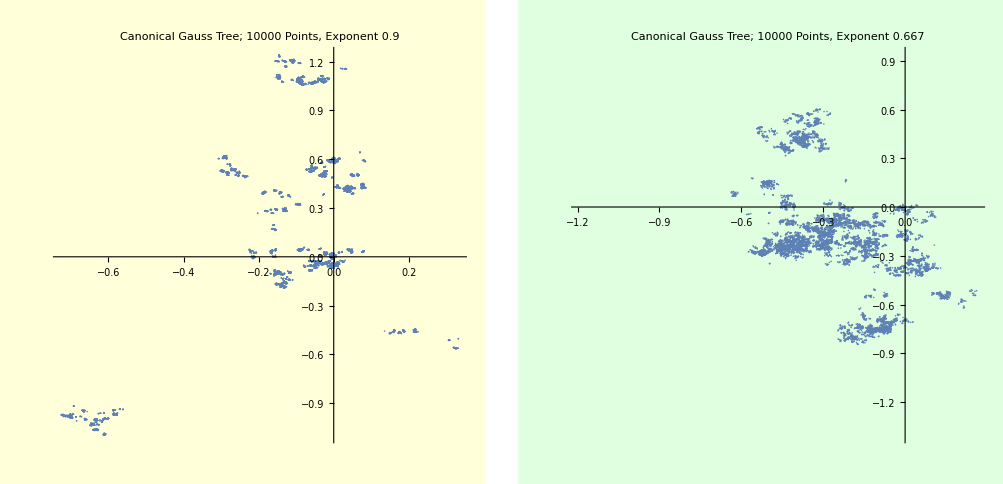

```mathematica
n1 = 10000;
r1 = 0.9;
r2 = 0.667;
Timing[
G1=Graph[canonicalGaussTree[n1,r1]];
G2=Graph[canonicalGaussTree[n1,r2]];
]
lpr1 = ListPlot[VertexList[G1] , Background->LightYellow,AspectRatio->1.0,
PlotLabel->Row[{"Canonical Gauss Tree; ",n1, " Points, Exponent ",r1   }]];
lpr2 = ListPlot[VertexList[G2] , Background->LightGreen,AspectRatio->1.0,
PlotLabel->Row[{"Canonical Gauss Tree; ",n1, " Points, Exponent ",r2   }]];
GraphicsRow[{lpr1,lpr2}]
```

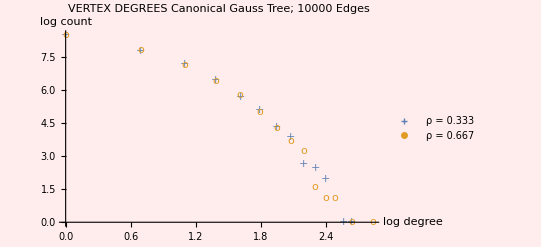

```mathematica
dataVtxDeg1 = Sort[Tally[VertexDegree[G1]]];
dataVtxDeg2 = Sort[Tally[VertexDegree[G2]]];

ListPlot[{Log[dataVtxDeg2], Log[dataVtxDeg1]},
Background->LightPink,
AxesLabel->{"log\ndegree", "log\ncount"},
PlotLegends->{ Row[{"ρ = ",r2}],Row[{"ρ = ",r1}]},
PlotMarkers->{"+","o"},
PlotLabel->Row[{"VERTEX DEGREES\nCanonical Gauss Tree; ",n1, " Edges"  }]
]
```

### Section.Subsection DEPRECATED: Less efficient time-dependent rejection sampling of points in Unit Disk

```mathematica
(* acceptance rate when k points already exist, nearest at distance Δ: NOT SAME AS AGORAPHOBIC P.P. *)
acceptanceRate[Δ_, θ_,k_]:=N[θ /(θ+k)+ (k/(θ+k))*Exp[-Δ*k]];
```

```mathematica
(* point (0,0) is inserted before other n = nPlacesExceptZero points *)
agoraphobicPointProcess[n_,θ_]:=Module[{X,accept, Δ,ρ,ζ,x,y,k},
X = Table[{0,0},{n+1}];
For[k = 1, k≤n, k++,
accept = False;
While[¬accept,
ρ=Sqrt[RandomReal[]];
ζ=RandomReal[{0.0, 2*Pi}];
(* Random point in unit disk *)
{x,y} = {ρ*Cos[ζ], ρ*Sin[ζ]};
(* Least distance to previous points *)
Δ = Min[Map[Norm[{x,y} - #]&, Take[X, k] ] ];
(* random rejection sampling *)
If[RandomReal[]≤acceptanceRate[Δ, θ,k], accept = True];
];
X[[k+1]] = {x, y};
];
Return[X];
];
```

{7.10792,Null}

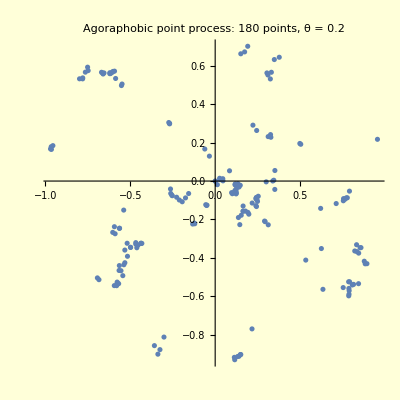

```mathematica
n = 180;
θ = 0.2;
Timing[
X = agoraphobicPointProcess[n,θ];
]

lp0 = ListPlot[X, AspectRatio->1.0, Background->LightYellow,
PlotLabel->Row[{"Agoraphobic point process: ", n, " points, θ = ",θ}]
]
```

## Section. Full Simulator: Retropreferential Process, Sporadic Reports

### Section.Subsection Build Points & Trajectory (needs Global Parameters)

```mathematica
Timing[
G = Graph[agoraphobicPointsHardThreshold[nPlacesExceptZero ,θ,ρ] ];
]
X = VertexList[G];

Timing[
trajectory=retropreferentialMotion[X,ϕ,nSteps];
]

Timing[
{sporadicReports,sojournHistory}=sporadicReporter[X,trajectory];
]
```

{0.333949,Null}

{309.589,Null}

{10.2614,Null}

```mathematica
Print["# possible sites to visit = ", Dimensions[X] ];
Print["# distinct sites visited = ", Length[Union[trajectory]] ];
Print["# reports = ", Length[sporadicReports] ];
Print["# time span = ", Last[sojournHistory] [[3]] ];
rpt = RandomChoice[sporadicReports];
Print["typical report: ", rpt, " refers to point ", X[[rpt[[2]] ]] ];

locationsVisited = Union[trajectory];
ListPlot[{X[[locationsVisited ]], X[[Complement[Range[ Length[X]], locationsVisited ] ]]},
PlotLegends->{"Visited", "Unvisited"},
PlotMarkers->{"+","o"},
AspectRatio->1.0,
PlotLabel->Row[{Length[Union[trajectory]]," out of ",Length[X] , " locations visited after ", s , " steps."}],
Background->LightYellow]
```

# possible sites to visit = {301,2}

# distinct sites visited = 94

# reports = 2129

# time span = 79.5586

typical report: {38.7569,36} refers to point {0.744926,-0.337359}

-Graphics-

## Section. Experiments

### Section.Subsection Example: Uniform Points

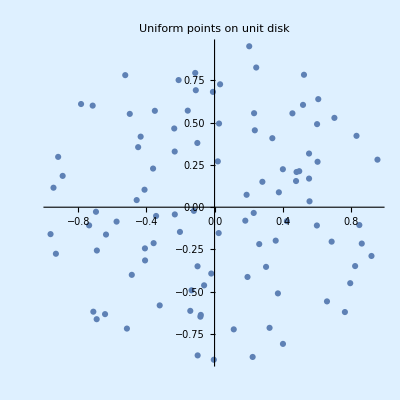

```mathematica
(* Select uniform points in disk *)
n = 100;
Y =Select[RandomReal[{-1.0, 1.0}, {Round[n*4/Pi], 2}], Norm[#]<1.0&];
uniformPlot = ListPlot[Y , AspectRatio->1.0,Background->LightBlue, PlotLabel->"Uniform points on unit disk"]
```

### Section.Subsection Display Spanning Tree

{1.51177,Null}

{1.3378,Null}

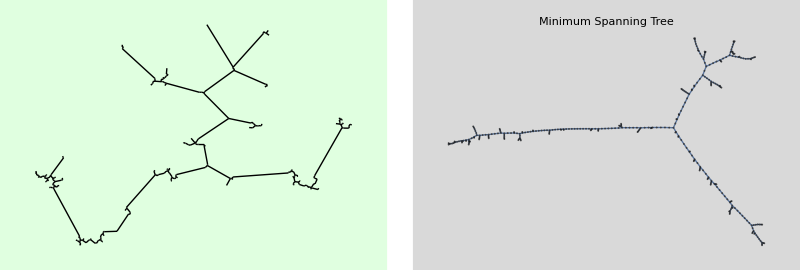

```mathematica
nV = Length[X];
(* Here are the graph edges *)
Timing[
sortedEdgeWeights = edgeWeights[X];
]
Timing[
𝒯 = minWeightSpanningTree[nV,sortedEdgeWeights];
]
mwst = Show[𝒯 , Background->LightGray, PlotLabel->"Minimum Spanning Tree"];

𝒱=VertexList[𝒯 ];
mwstEuclideanEmbed = Graphics[Map[Line[{First[#],Last[#] }]&,  EdgeList[𝒯 ] ]  ,
Background->LightGreen];
Show[GraphicsRow[{ mwstEuclideanEmbed, mwst}]]
```

### Section.Subsection Graph Made out of Inverse Square Distance Sampled Edges

{1.49377,Null}

{{-0.78548,-0.764796}<->{-0.202271,0.517059},1.40829}

1416

4.51019

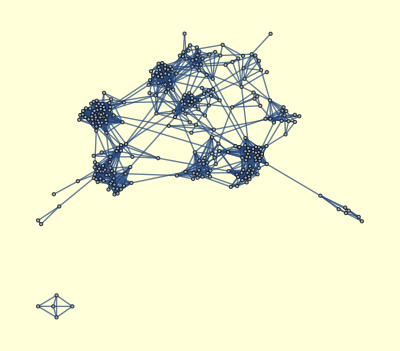

```mathematica
Timing[
sortedEdgeWeights = edgeWeights[X];
]
RandomChoice[sortedEdgeWeights]
(* mean vertex degree *)
μ = 9.4103;
desiredEdgeCount = Round[Length[X]*μ/2.0]
(* inverse square distance weighting *)
weights = 1.0/sortedEdgeWeights[[All, 2]]^2;
RandomChoice[weights]
(* sample desired # edges with this weight function *)
ℰX = RandomSample[weights->sortedEdgeWeights, desiredEdgeCount][[All, 1]];
𝒢X = Graph[ℰX , Background->LightYellow ]
```

## Section. Retro-preferential Visit Process

### Section.Subsection Trajectory: Transitions with Memory of Past States

{211,2}

{16.9464,Null}

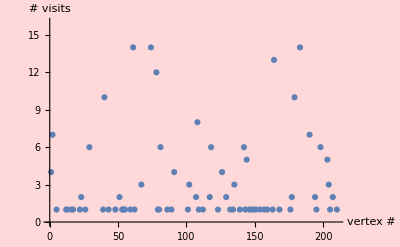

```mathematica
Dimensions[X]
η = 13.75; (* parameter > 0 *)
s = 360; (* desired # steps, which is Length[trajectory] - 1 *)
Timing[
trajectory=retropreferentialMotion[X,η,s];
]
ListPlot[Tally[trajectory] ,
Background->LightRed, 
AxesLabel->{"vertex #", "# visits"}
]
```

### Section.Subsection Trajectory Statistics: Vertex Degree Heavy Tails

Out of 301 locations, 94 have been visited after 431 steps

{4,2,5,4,1,1,5,17,1,9,2,8,2,1,4,2,17,17,1,6,1,1,3,2,5,1,3,1,1,9,1,4,1,5,7,1,11,38,35,1,1,1,6,10,1,1,1,1,1,1,1,1,1,13,1,27,19,3,2,2,1,5,1,6,2,1,1,9,2,1,1,2,2,1,1,16,16,7,2,1,2,1,1,1,1,2,2,1,1,3,1,1,1,1}

{{1,45},{2,15},{5,5},{3,4},{4,4},{6,3},{9,3},{17,3},{16,2},{7,2},{19,1},{27,1},{13,1},{10,1},{35,1},{38,1},{11,1},{8,1}}

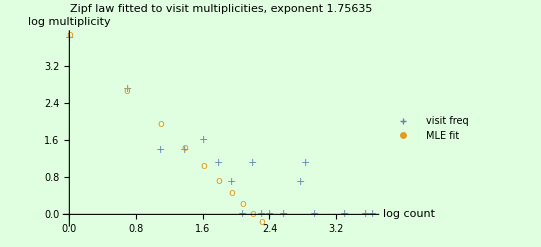

-Graphics-

```mathematica
Print["Out of ", Length[X], " locations, ", Length[Union[trajectory]], " have been visited after ", Length[trajectory] , " steps"];

visitFrequencies = Tally[trajectory][[All, 2]]

visitTally = Sort[Tally[visitFrequencies], #1[[2]]>#2[[2]]& ]
{paramFitVF, dataFitVF} = fitZipf[visitFrequencies];
ListPlot[{Log[N[  visitTally] ],Log[ dataFitVF]},
Background->LightGreen, 
AxesLabel->{ "log\ncount","log\nmultiplicity"},
PlotLegends->{"visit freq", "MLE fit"},
PlotMarkers->{"+","o"},
PlotLabel->Row[{"Zipf law fitted to visit multiplicities, exponent ", paramFitVF}],
PlotRange->All
]

locationsVisited = Union[trajectory];
ListPlot[{X[[locationsVisited ]], X[[Complement[Range[ Length[X]], locationsVisited ] ]]},
PlotLegends->{"Visited", "Unvisited"},
PlotMarkers->{"+","o"},
AspectRatio->1.0,
PlotLabel->Row[{Length[Union[trajectory]]," out of ",Length[X] , " locations visited after ", s , " steps."}],
Background->LightYellow]
```

## Section. Simulator Development & Diagnostics

### Section.Subsection Simulate Motion Times (Z_i) - Truncated Pareto

```mathematica
distanceList=Map[Norm, Differences[X[[trajectory]] ] ];
γ = 1.0 - (1.0/cMotion)^αMotion;
(* simulate truncated Pareto *)
Z = Table[(1.0/maxSpeed)*distanceList[[j]]/((1.0 - γ*RandomReal[])^(1.0/αMotion)), {j, 1, nSteps} ];
{RandomChoice[Z],Min[Z],Max[Z],Mean[Z]}
```

{1.2439,0.00141564,6.7063,0.222627}

### Section.Subsection Simulate Report Counts per Sojourn (R_i), & Gaps (U_j^k) During Sojourn - Truncated Zipf / Pareto

```mathematica
atLeastOneReport = RandomVariate[BernoulliDistribution[ηReports],Length[trajectory] ];
uncensoredReportCounts = RandomVariate[ZipfDistribution[cReports,sReports - 1], Length[trajectory]];
reportCounts = atLeastOneReport*uncensoredReportCounts ;
Take[reportCounts, 20]
Print["Total # reports = ", Total[reportCounts ] ];
κ=1.0 - (1.0/cSojourn)^βSojourn;
fineIntervals = Table[
(* simulate truncated Pareto *)
Table[minSojourn/((1.0 - κ*RandomReal[])^(1.0/βSojourn)), {reportCounts[[j]]+1} ], {j, 1, Length[trajectory] }];
```

{1,31,1,1,1,2,1,1,16,3,1,1,1,1,0,4,0,1,1,1}

Total # reports = 2096

```mathematica
(* Diagnostics *)
k1 = RandomInteger[{1,Length[reportCounts]}];
Print["With ",reportCounts[[k1]], " reports, fine intervals look like ", fineIntervals[[k1]] ];
Print["Total Motion Time = ", Total[Z] ];
Print["Total Sojourn Time = ",  Total[Flatten[fineIntervals ]] ];
```

With 1 reports, fine intervals look like {0.000112346,0.00015373}

Total Motion Time = 95.7296

Total Sojourn Time = 14.8876

### Section.Subsection Simulate Entire Report Set, Seasonally Adjusted, with Corrupted Location Values

```mathematica
(* sojourn intervals *)
Y = Map[Total, fineIntervals ];
Print["Y looks like: ",{RandomChoice[Y], Length[Y], Total[Y]}];
Print["Z looks like: ",{RandomChoice[Z], Length[Z], Total[Z]}];

Ycumulative = Accumulate[Y];
Zcumulative = Accumulate[Z];
(* arrival Times *)
sojournStarts = Prepend[Drop[Ycumulative, -1]+Zcumulative , 0.0];

(* corrupt the trajectory *)
corruptedTrajectory = Table[If[RandomReal[]< corruptionRate, RandomInteger[{1, Length[X]}],trajectory[[j]] ],
{j, 1, Length[trajectory] }];
Print["# corrupted locations = ", Length[trajectory]-Count[corruptedTrajectory -trajectory, 0] ];
Print["expected # = ", nSteps*corruptionRate];
(* uses corrupted trajectory and seasonally adjusted report times *)
sporadicReports = Flatten[Table[If[reportCounts[[j]]≥1,
{seasonAdjust[sojournStarts [[j]]+fineIntervals[[j, k]] ],corruptedTrajectory[[j]]}], 
{j, 1, Length[trajectory]}, {k, 1, reportCounts[[j]] }], 1];

RandomChoice[sporadicReports]
```

Y looks like: {0.00735747,431,14.8876}

Z looks like: {0.013346,430,95.7296}

# corrupted locations = 13

expected # = 10.75

{88.705,159}

### Section.Subsection Reveal True Trajectory

```mathematica
(* departure Times *)
sojournEnds = Prepend[Drop[Ycumulative, 1]+Zcumulative , First[Y]];

(* list of 3-ples of form (placeID, time-entered, time departed) *)
sojournHistory = Transpose[{trajectory,Map[seasonAdjust, sojournStarts], Map[seasonAdjust,sojournEnds]}];
Take[sojournHistory, 3]

(* list of 4-ples of form (x, y, time-entered, time departed) *)
sojournHistoryXY = Map[{X[[#[[1]] ]], #[[2]], #[[3]]}&, sojournHistory];
Take[sojournHistoryXY, 3]
```

{{1,0.,0.0530863},{224,0.353494,0.47392},{242,0.484173,0.504771}}

{{{0.,0.},0.,0.0530863},{{-0.00878178,-0.00673585},0.353494,0.47392},{{0.00420517,-0.00263952},0.484173,0.504771}}

### Section.Subsection Diagnostic: Cumulative Distinct Points Visited

Predicted # = 96.9841

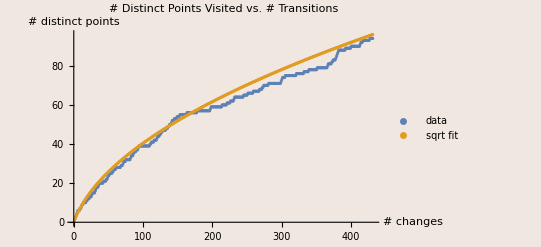

```mathematica
Print["Predicted # = ",Sqrt[2*ϕ*Length[trajectory] + ϕ^2]-ϕ+1 ];
cumulativeNumPtsVisited=Table[{j, Length[Union[Take[trajectory , j]]]}, {j, 1, Length[trajectory]}];
odeFitValues =  Table[{t,Sqrt[2*ϕ*t + ϕ^2]-ϕ}, {t, 1, Length[trajectory]}] ;
ListPlot[{cumulativeNumPtsVisited,odeFitValues },
Background->LightBrown,
AxesLabel->{"# changes","# distinct\npoints"},
PlotLabel->"# Distinct Points Visited vs. # Transitions",
PlotLegends->{"data","sqrt\nfit"}
]
```

### Section.Subsection Diagnostic: Motion Times

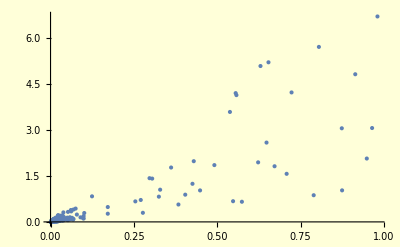

```mathematica
ListPlot[Transpose[{distanceList, Z}] ,PlotRange->All, Background->LightYellow]
```

### Section.Subsection Diagnostic: Seasonality

5.28455

True

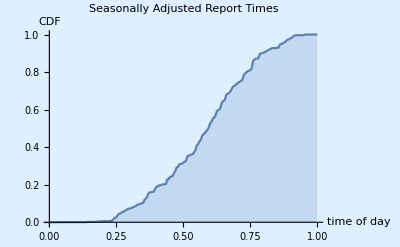

```mathematica
tDat = sporadicReports[[All, 1]];
RandomChoice[tDat]
Length[tDat]==Total[reportCounts ]
reportTimesOfDay = Map[#-Floor[#]&, tDat];
dailyDist = EmpiricalDistribution[reportTimesOfDay];
DiscretePlot[CDF[dailyDist, t], {t, 0.0,1.0, 0.005},
Background->LightBlue,
PlotLabel->"Seasonally Adjusted Report Times",
AxesLabel->{"time of day","CDF"}]
```

### Section.Subsection Diagnostic: Times of Sojourn Starts

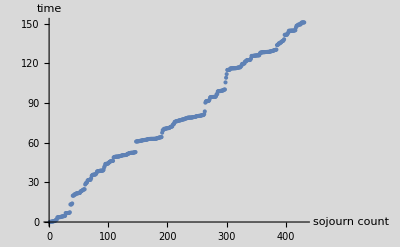

```mathematica
lpsojourns =ListPlot[sojournStarts,
Background->LightGray,
AxesLabel->{"sojourn\ncount", "time"}]
```

### Section.Subsection Diagnostic: 3-Dimensional (x,y,t) Plot of Reported Locations

```mathematica
reportedTrajectory = Map[Flatten[{ X[[#[[2]] ]],#[[1]]}]& , sporadicReports ] ;
RandomChoice[reportedTrajectory]
ListPointPlot3D[reportedTrajectory , ColorFunction->"Rainbow",
AxesLabel->{"x", "y", "t"}]
```

{0.744926,-0.337359,70.2865}

-Graphics3D-

### Section.Subsection Diagnostic: Sojourn Lengths vs. Report Counts

{{431},{431}}

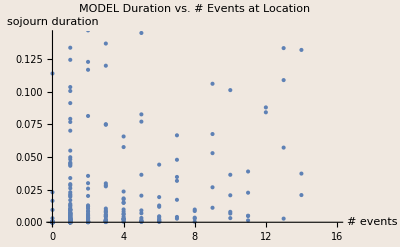

```mathematica
{Dimensions[Y],Dimensions[reportCounts]}
ListPlot[Transpose[{reportCounts, Y}], 
AxesLabel->{"# events", "sojourn\nduration"},
Background->LightBrown,
PlotLabel->"MODEL\nDuration vs. # Events at Location"]
```

### Section.Subsection Diagnostic: Sojourns of Retro-Preferential process

{192,163,36,38,257,107,249,299,127,67,126,7,87,158,203,8,183,186,101,180,29,265,274,289,89,242,85,205,14,1,220,236,44,58,240,146,159,291,260,124,26,254,71,293,201,64,213,72,224,269,13,283,35,18,47,11,96,19,196,134,271,137,259,41,223,178,81,28,145,84,16,34,195,225,188,253,10,270,177,273,210,241,191,12,78,114,268,218,279,198,148,57,194,130}

0

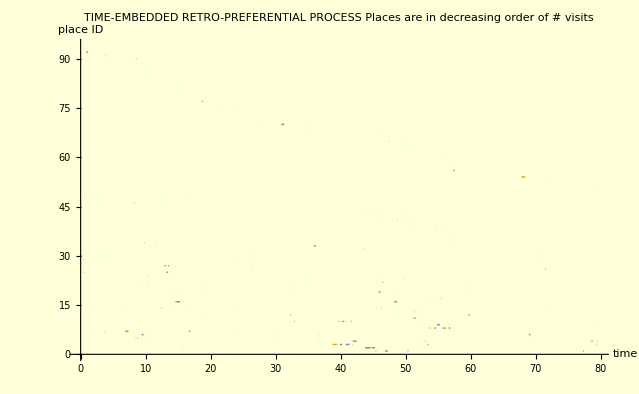

```mathematica
(* relabel points *)
pointsByDescFreq = Sort[Tally[trajectory], #1[[2]]>#2[[2]]&][[All, 1]]
pointLookUp = SparseArray[
Join[Table[pointsByDescFreq [[j]]->j, {j, 1, Length[pointsByDescFreq] }],
Map[#->0&, Complement[Range[nPlacesExceptZero], Union[trajectory] ]
]
]
];
pointLookUp [[RandomInteger[{1, nPlacesExceptZero}] ]]

(* vertical axis has places in decreasing frequency order *)
sojournsAsLines = Map[{{#[[2]], pointLookUp [[#[[1]]  ]]}, { #[[3]],pointLookUp [[#[[1]]  ]] } }&, sojournHistory];

ListLinePlot[sojournsAsLines,
PlotLabel->"TIME-EMBEDDED RETRO-PREFERENTIAL PROCESS\nPlaces are in decreasing order of # visits",
AxesLabel->{"time", "place\nID"},
PlotStyle->Thick,
Background->LightYellow]
```